1(a)

```mathematica
Manipulate[x1=1.1;X=Table[Nest[# ⅇ^(A(1-#))&,x1,t],{t,0,49}];{ListLinePlot[X],Text[Mean[X]]},{A,{2.0,2.3,2.6,3.14}}]
```

1(b)

```mathematica
x1=1.1;
y1=1.0;
A=2.3;
```

```mathematica
Manipulate[X=Table[Nest[# ⅇ^(A(1-#))&,x1,t],{t,0,49}];Y=Table[Nest[X[[t]] # ⅇ^(B(1-#))&,y1,t],{t,0,49}];ListLinePlot[Table[{X[[i]],Y[[i]]},{i,Length[X]}],AxesLabel->{x,y}],{B,1.5,3.5}]
```

2(a)

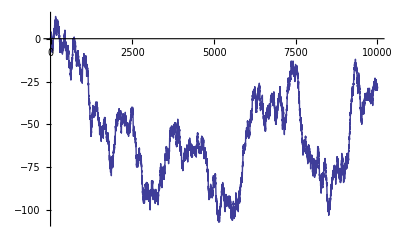

25

```mathematica
n=10000;
choose=RandomChoice[{-1,1},n];
X=Accumulate@choose;
ListLinePlot[X]
Y=Count[X,0]
```

3(a)

```mathematica
gtoadj[g_]:=Table[Table[If[MemberQ[g,{i,j}]||MemberQ[g,{j,i}],1,0],{i,g[[1]]}],{j,g[[1]]}]
gtest={6,{1,2},{1,3},{2,3},{4,5}}
gtoadj[gtest]//MatrixForm
```

{6,{1,2},{1,3},{2,3},{4,5}}

(0 | 1 | 1 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
adjtog[a_]:=List[Length[a],Table[If[a[[i,j]]==1,{i,j},Null],{i,Length[a]},{j,i,Length[a]}]]
adjtog[a_]:=Flatten[List[Length[a],Select[Position[a,1],#[[1]]≤#[[2]]&]],1]
atest=({{0, 1, 1, 0, 0, 0}, {1, 0, 1, 0, 0, 0}, {1, 1, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0}});
adjtog[atest]
```

{6,{1,2},{1,3},{2,3},{4,5}}